# the workload test part 2

```mathematica
SetDirectory[NotebookDirectory[]];
rl[d_]:=Placed[d,Axis,Rotate[#,Pi/2]&]
SwapLoad[file_String]:=Import["../dataset/"<>file][[3;;All,5]]
VMLoad[file_String]:=Import["../dataset/"<>file][[4;;,{3,5,7}]]
TableLoad[f_,c_Integer]:=Table[f[ToString[i]],{i,1,c}]
MakeList[l1_List,l2_List,direction_List]:=Table[{1,
If[direction[[i]]>0,l2[[i]]/l1[[i]],l1[[i]]/l2[[i]]]}
,{i,Length[direction]}]
```

## dynamic tau redo all test

### 3-8 dynamic tau

key | value | key | value
N | 5GB | init mem | 512MB
VM count | 10 | f | 150MB
high load | 200MB | □ | □

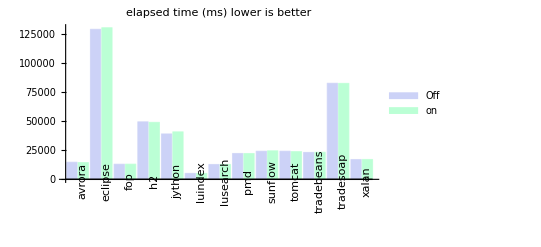

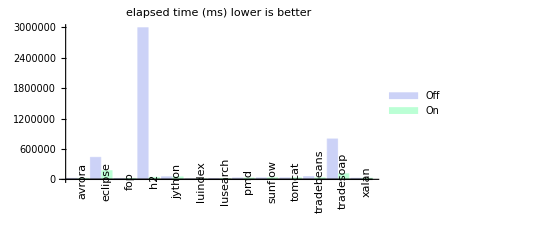

(ms) | off | on
avrora | 18238 | 17358
eclipse | 433186 | 171196
fop | 16029 | 17748
h2 | 2991145 | 37778
jython | 49847 | 47796
luindex | 6268 | 6144
lusearch | 15821 | 16029
pmd | 27475 | 26530
sunflow | 29067 | 30805
tomcat | 29034 | 29370
tradebeans | 54152 | 29416
tradesoap | 796455 | 110001
xalan | 21351 | 22948
sum | 4488068 | 563119

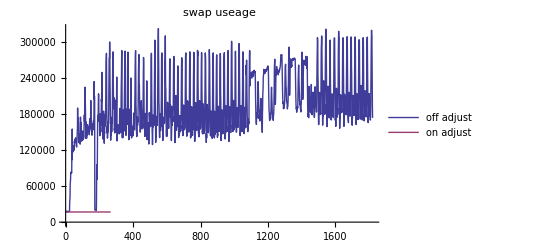

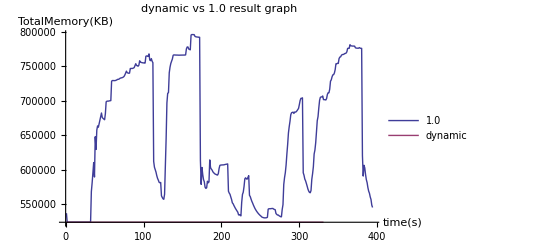

```mathematica
dp=Import["../dataset/3-8_dacapo/dacapo.ods"][[1]];
swapoff=SwapLoad["3-8_dacapo/off-swap.log"];
swapon=SwapLoad["3-8_dacapo/on-swap.log"];
hi=VMLoad["3-8_dacapo/high-2.log"];
low=VMLoad["3-8_dacapo/low-2.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
BarChart[dp[[2;;-2,4;;5]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","On"},PlotLabel->"elapsed time (ms) lower is better"]
Grid[dp[[All,{1,4,5}]],Frame->All]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]],low[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi,low]
```

配置512MB内存,运行时间相差非常大,而且几乎无法看到开启调节的柱状图.
而且SWAP分区使用率也是非常的夸张.
这个只能说是对于人而言.没有美观的感觉.但是对于系统而言是正常的结果.
我们需要接受它,当然.在论文中不使用这组数据.

### 3-9 dynamic tau high

key | value | key | value
N | 10GB | init mem | 1GB
VM count | 10 | f | 150MB
high load | 800MB | □ | □

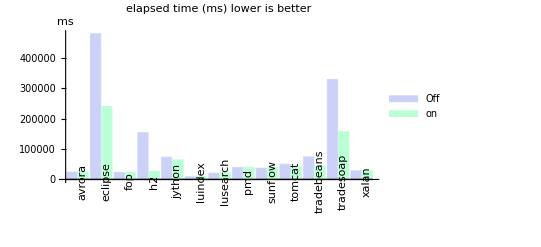

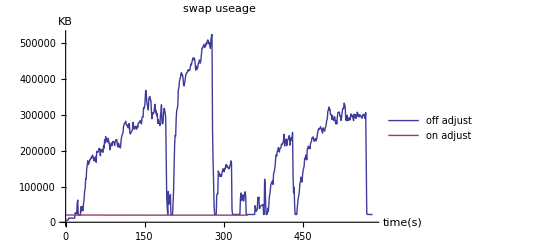

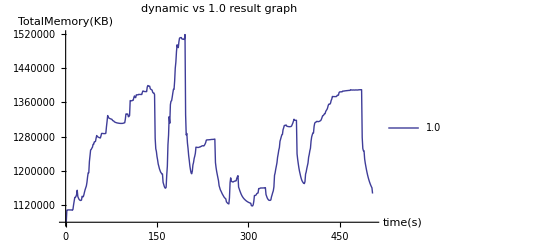

```mathematica
dp=Import["../dataset/3-9_dacapo_high/dacapo.ods"][[1]];
swapoff=SwapLoad["3-9_dacapo_high/off-swap.log"];
swapon=SwapLoad["3-9_dacapo_high/on-swap.log"];
hi=VMLoad["3-9_dacapo_high/high-10.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better",
AxesLabel->"ms"
]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",AxesLabel->{"time(s)","KB"},
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi]
```

结论和以前的类似.

## multi vm test

### 测试方法

首先分为两个大组,一个大组是开启调节的测试,一个大组是关闭调节的测试.
每个大组安排每个虚拟机上运行不同性质的测试.为了保证满足调节条件.需要安排
每个大组至少有一台以上的vm运行内存密集程序,称为目标机.至少有一台以上的vm运行非内存密集程序
(如CPU密集和磁盘密集).为了使得运行非内存密集的vm把内存贡献给目标机.
同时,每台vm在测试的时候还需要执行记录swap的程序.在开启调节的时候需要记录每台虚拟机分配的内存.

内存型密集程序可以选择dacapo测试集中的h2,...因为目前只找到dacapo测试集的这几个测试属于内存密集型.
非内存密集型可以选择phoronix-test-suite测试框架中的许多程序如:
nginx
...

因为每个测试运行的时间都不一样.所以规定以单次测试时间最长的测试所运行的时间作为该大组测试的时间.
对于单次运行时间不足的测试采用循环运行的方式.当运行时间超过该大组的测试时间时候强制手工杀死测试进程.
因为最后一次运行时间不足一个完整的周期所以该次测试成绩无效.对于之前运行的所有测试成绩(包括循环运行的所有有效成绩)取平均值作为该项测试的成绩.

最后将两大组的每个测试的成绩相除,换算成百分比.以不开启调节为基准1.因为一些测试成绩是越高越好,一些成绩是越低越好.
所以需要注意除以的方向

### 3-22 2vm test

N | 1G | init men | 512MB
vmcount | 2 | f | 120M
vm1 | nginx | high load | 0
vm2 | h2 | high load | 100MB

| vm1 | vm2
 | nginx | h2
unit | request/s | ms
off | 6589.78 | 110753
on | 6488.57 | 42207

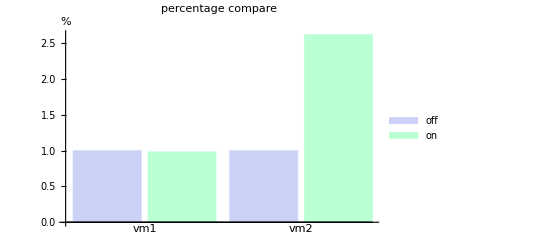

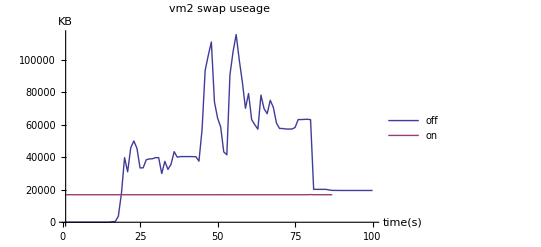

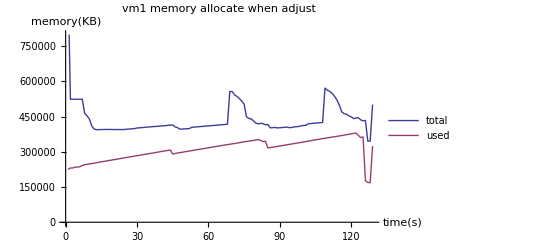

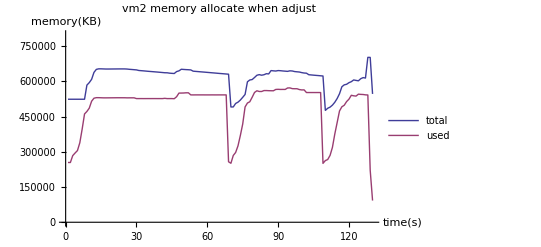

```mathematica
table=Import["../dataset/3-22/statics.ods"][[1]];
offswap={None,SwapLoad["3-22/vm2/off-swap.log"]};
onswap={SwapLoad["3-22/vm1/on-swap.log"],SwapLoad["3-22/vm2/on-swap.log"]};
onmem={VMLoad["3-22/vm1/on.log"],VMLoad["3-22/vm2/on.log"]};
Grid[table[[1;;-2]],Frame->All]
BarChart[{{1,table[[5,2]]/table[[4,2]]},{1,table[[4,3]]/table[[5,3]]}},
PlotLabel->"percentage compare",ChartLegends->{"off","on"},
ChartLabels->{{"vm1","vm2"},None},AxesLabel->"%"
]
ListLinePlot[{offswap[[2,1;;-40]],onswap[[2]]},
PlotRange->All,PlotLabel->"vm2 swap useage ",PlotLegends->{"off","on"},
AxesLabel->{"time(s)","KB"}
]
ListLinePlot[{onmem[[1,All,1]],onmem[[1,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm1 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
ListLinePlot[{onmem[[2,All,1]],onmem[[2,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm2 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
Clear[table,offswap,onswap,onmem]
```

对于两台虚拟机的测试,可以看到结果是类似的.主要依然表现为以下几个方面:
图1:
-    对于非内存密集型的程序.性能会有所下降.但是下降的数量不大.
-    对于内存密集型的程序.因为保证了分配足够的内存.所以相对于不开启调节的性能有提升许多
图2:
-    不开启调节的vm2占用大量的swap.(vm1因为不需要太多内存,所以始终没有使用swap).
-    开启了调节之后vm2就不再使用swap了.(从途中可以看到swap一直保持一个数,这是因为不开启调节的测试是紧接着上一个测试的)
-    两者运行的时间相差无几.这是因为整个测试以最长的时间为基准(vm1上单次运行需要的时间)
      vm2上其实完整的执行了2次
图3,图4:
-   对于vm1可以看到,分为3个阶段.其实是3次测试,phoronix-test-suite默认运行3次求平均值作为最后结果.
    三次测试内存需求逐渐升高.
-   对于vm2可以看到,分为2个完整的测试和一个不完整的测试.因为dacapo只运行1次.所以当第一次运行结束之后,
    就通过外部的脚本的循环,进行下一个周期,而且明显的可以看到第二次运行的时间比第一次短得多.关于这一点目前还没有能力解释.
    当第3次还没有运行完成之后.vm1就结束了.所以这里手工杀死测试进程.
    
2台虚拟机的测试还不能说明什么问题.
下面的5台虚拟机和10台虚拟机能够更加深刻的说明问题.

### 03-24 5vm test

N | 2.5G | init men | 512MB
vmcount | 5 | f | 120M

安排5台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | nginx | cpu | 0 | Reqeust/s
vm2 | tradebeans | mem | 100MB | ms
vm3 | build-mplayer | cpu | 0 | s
vm4 | tradesoap | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s

```mathematica
{table,offraw,onraw}=Import["../dataset/3-24/statics.xlsx"];
offswap=TableLoad[SwapLoad["3-24/vm"<>#<>"/off-swap.log"]&,5];
onswap=TableLoad[SwapLoad["3-24/vm"<>#<>"/on-swap.log"]&,5];
onmem=TableLoad[VMLoad["3-24/vm"<>#<>"/on-mem.log"]&,5];
```

如图:下面是取平均之后的测试结果表格

```mathematica
Grid[table[[1;;-2]],Frame->All]
```

id | nginx | tradebeans | build-mplayer | tradesoap | pgbench
intensive | cpu | mem | cpu | mem | disk
unit | request/s | ms | s | ms | TPS
off | 6432.33 | 26163.6 | 576.933 | 109978. | 93.55
on | 6103.59 | 25830. | 626.16 | 95930.8 | 118.493

为了更清楚的看到它们的比例,下面画出条形图:

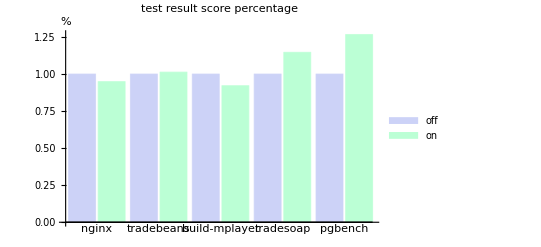

```mathematica
BarChart[MakeList[table[[4,2;;]],table[[5,2;;]],{1,-1,-1,-1,1}],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{table[[1,2;;]],None},AxesLabel->"%"
]
```

可以看到测试成绩提高依次排序为pgbench>tradesoap>tradebeans.
其中tradebeans和tradesoap都是内存密集型程序.符合我们的预期.
但是反而pgbench磁盘密集型程序提高最多.比较难于理解.

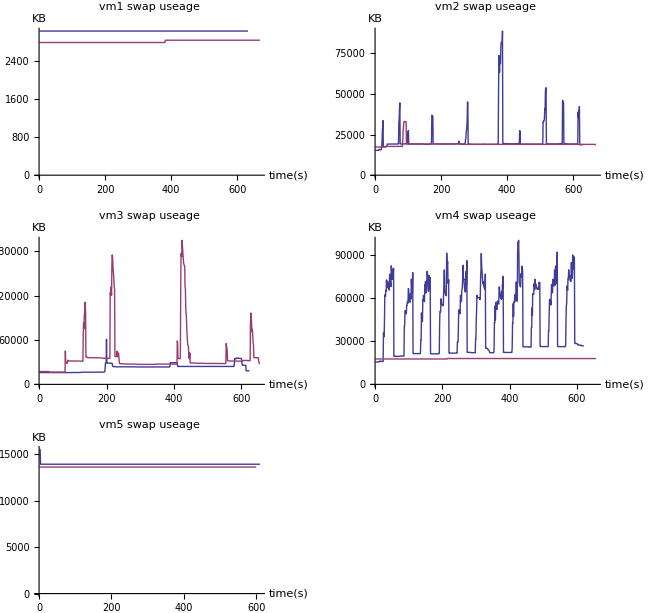

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

因为我们主要关心swap的情况,我们可以看到,除了build-mplayer测试开启调节后swap的使用量上升之外,
其他测试的swap使用量都减小到了合理的程度.特别是对于vm4效果非常明显.这也是vm4提分比较多的原因.
可以说明调节程序是基本达到了我们预期的效果.
编译程序的swap的反常其实是因为编译程序的内存使用是脉冲形状,在一小段时间里内存使用量迅速增加又迅速减小,超过了调节的精度.所以无法调节.
最后,磁盘密集型程序得分也高的原因,可以做一个猜想,因为之前大量的使用swap,导致I/O量大,磁盘工作不过来.而之后基本不使用swap了,磁盘能够集中精力处理pgbench的请求.所以分数也高了.

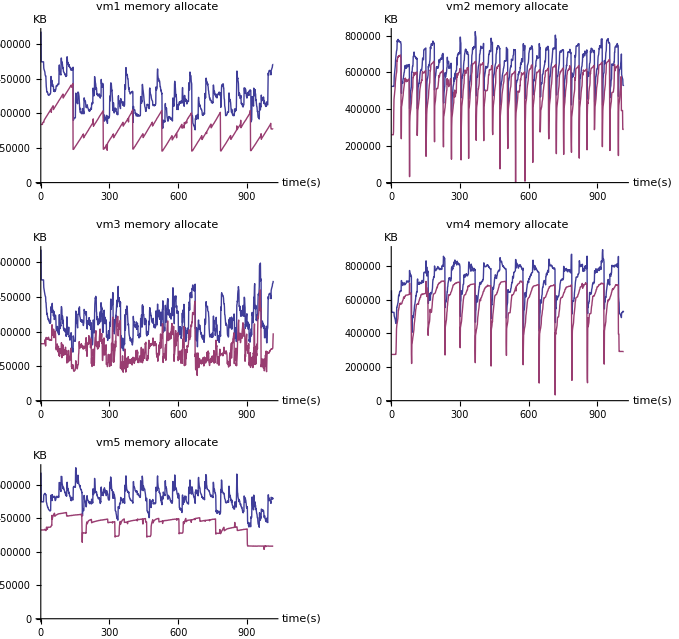

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

#### 附录:

关闭调节各个测试的详细分数列表:

```mathematica
Grid[offraw,Frame->All]
```

nginx | tradebeans | build-mplayer | tradesoap | pgbench
6404.01 | 25947. | 589.77 | 115837. | 98.12
6468.04 | 25913. | 569.91 | 104774. | 93.38
6470.55 | 27493. | 571.12 | 111566. | 89.96
6380.12 | 26646. |  | 114275. | 92.13
6533.53 | 25818. |  | 108938. | 94.16
6542.23 | 27082. |  | 114150. | 
6416.12 | 24898. |  | 110295. | 
6439.23 | 25631. |  | 119415. | 
6443.25 | 26037. |  | 102577. | 
6305.37 | 27581. |  | 105173. | 
6366.04 | 25591. |  | 102755. | 
6285.7 | 25440. |  |  | 
6511.87 | 25840. |  |  | 
6361.72 | 26198. |  |  | 
6428.31 | 25994. |  |  | 
6417.03 | 25997. |  |  | 
6516.57 | 25709. |  |  | 
6492.19 | 25550. |  |  | 
 | 25574. |  |  | 
 | 25448. |  |  | 
 | 28754. |  |  | 
 | 26459. |  |  |

开启调节后各个测试的详细分数表

```mathematica
Grid[onraw,Frame->All]
```

nginx | tradebeans | build-mplayer | tradesoap | pgbench
6040.82 | 27091. | 647.74 | 96508. | 113.29
5983.04 | 26628. | 622.26 | 97406. | 119.
6025.34 | 26376. | 608.48 | 97223. | 125.21
6009.15 | 26717. |  | 95176. | 123.13
6006.31 | 26808. |  | 95332. | 105.15
5946.25 | 26435. |  | 94357. | 125.18
6072.94 | 26654. |  | 95454. | 
6321.03 | 27436. |  | 96337. | 
6244.55 | 26446. |  | 95850. | 
6128.24 | 27611. |  | 95505. | 
6045.95 | 25585. |  | 95847. | 
6033.12 | 26875. |  | 95549. | 
6213.83 | 26058. |  | 96557. | 
6346.85 | 26809. |  |  | 
6364.43 | 25642. |  |  | 
6056.4 | 27181. |  |  | 
5972.76 | 2611. |  |  | 
6053.62 | 27475. |  |  | 
 | 26200. |  |  | 
 | 27609. |  |  | 
 | 25984. |  |  | 
 | 27521. |  |  | 
 | 25880. |  |  | 
 | 26752. |  |  | 
 | 26638. |  |  | 
 | 27899. |  |  | 
 | 26923. |  |  | 
 | 25396. |  |  |

### 03-27; 5vm test again

重新测试了一遍5vm的.得到类似的结论.到时候取一组即可.

```mathematica
{table,offraw,onraw}=Import["../dataset/3-27/statics.xlsx"];
offswap=TableLoad[SwapLoad["3-27/vm"<>#<>"/off-swap.log"]&,5];
onswap=TableLoad[SwapLoad["3-27/vm"<>#<>"/on-swap.log"]&,5];
onmem=TableLoad[VMLoad["3-27/vm"<>#<>"/on-mem.log"]&,5];
```

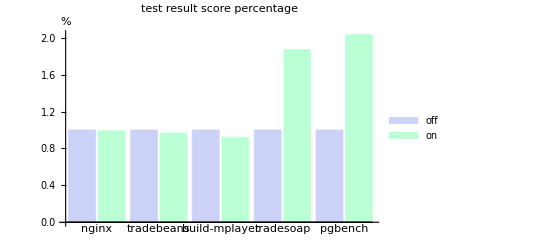

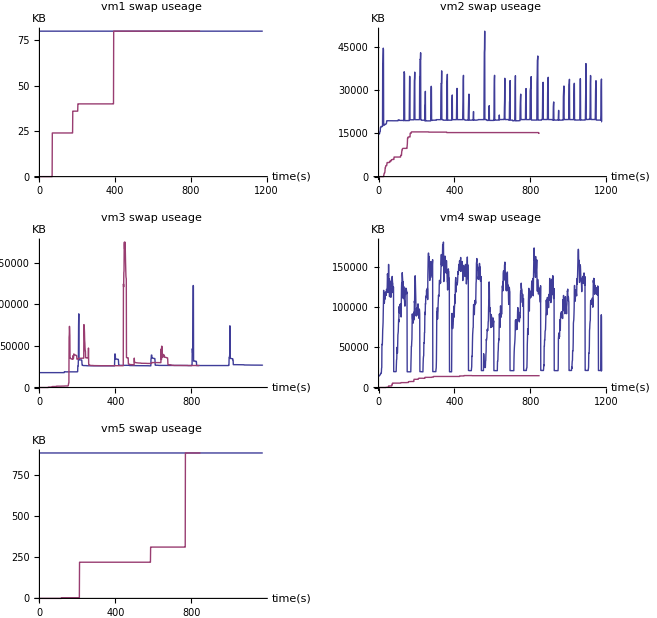

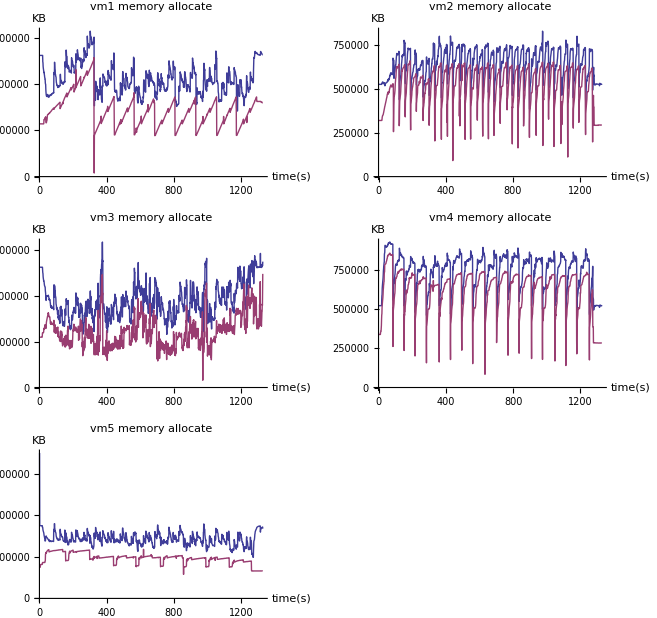

```mathematica
BarChart[MakeList[table[[4,2;;]],table[[5,2;;]],{1,-1,-1,-1,1}],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{table[[1,2;;]],None},AxesLabel->"%"
]
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

### 04-01;10 vm

N | 5G | init men | 512MB
vmcount | 10 | f | 120M

安排10台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | apache | cpu | 0 | Reqeust/s
vm2 | h2 | mem | 100MB | ms
vm3 | build-linux-kernel | cpu | 0 | s
vm4 | tradebeans | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s
vm6 | tradesoap | □ | □ | □
vm7 | john-the-ripper | □ | □ | □
vm8 | scimark2 | □ | □ | □
vm9 | openssl | □ | □ | □
vm10 | crafty | □ | □ | □

```mathematica
{table,offraw,onraw}=Import["../dataset/4-01/statics.xlsx"];
label=table[[1,{2,3,4,5,6,7,8,11,17,18}]];
offswap=TableLoad[SwapLoad["4-01/vm"<>#<>"/off-swap.log"]&,10];
onswap=TableLoad[SwapLoad["4-01/vm"<>#<>"/on-swap.log"]&,10];
onmem=TableLoad[VMLoad["4-01/vm"<>#<>"/on-mem.log"]&,10];
```

```mathematica
Grid[table[[1;;-2]]ᵀ,Frame->All]
```

id | sub id | intensive | load | unit | off | on
apache |  | cpu | 0. | request/s | 2702.31 | 2632.62
h2 |  | mem | 0. | ms | 123209. | 32645.5
Build-linux-kernel |  | cpu | 0. | s | 1061.81 | 1197.62
tradebeans |  | mem | 100M | ms | 26426. | 28727.5
pgbench |  | disk | 0. | TPS | 88.091 | 109.003
tradesoap |  | mem | 100M | ms | 111204. | 100578.
John-the-ripper | Blowfish | cpu | 0. | real C/S | 546. | 530.
 | Traditional DES | cpu | 0. | real C/S | 1.87267×10^6 | 2.01667×10^6
 | MD5 | cpu | 0. | real C/S | 17724. | 16572.2
scimark2 | Composite | cpu | 100M | Mflops | 423.273 | 391.655
 | Monte Carlo | cpu | 100M | Mflops | 161.595 | 161.498
 | Fast Fourier Transform | cpu | 100M | Mflops | 38.2575 | 33.7475
 | Sparse Matrix Multiply | cpu | 100M | Mflops | 482.323 | 382.73
 | Dense LU Matrix Factorization | cpu | 100M | Mflops | 997.03 | 951.218
 | Jacobi Successive Over-Relaxation | cpu | 100M | Mflops | 431.89 | 428.423
openssl |  | cpu | 0. | score | 52.0162 | 51.9261
crafty |  | cpu | 0. | s | 220.058 | 217.493

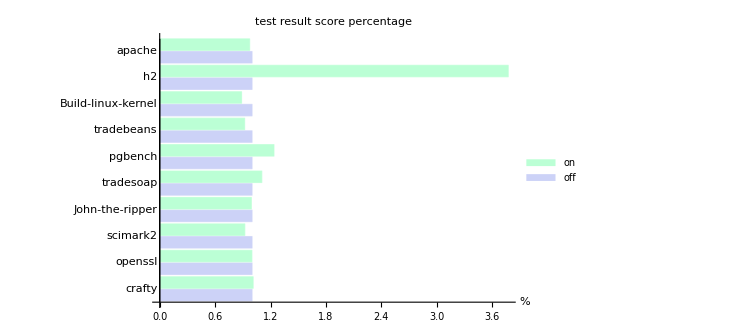

```mathematica
bar=
MakeList[table[[6,2;;7]],table[[7,2;;7]],{1,-1,-1,-1,1,-1}]~
Join~
{
{1,GeometricMean[table[[7,8;;10]]/table[[6,8;;10]]]},
{1,GeometricMean[table[[7,11;;16]]/table[[6,11;;16]]]}
}~
Join~
MakeList[table[[6,17;;18]],table[[7,17;;18]],{1,-1}];
BarChart[Reverse[bar],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{Reverse[label],None},AxesLabel->"%",BarOrigin->Left
]
```

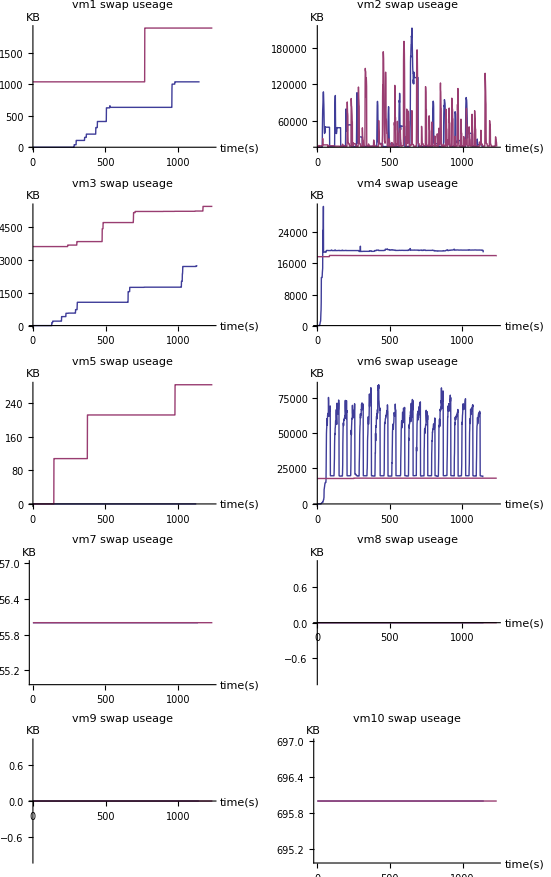

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->All,PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

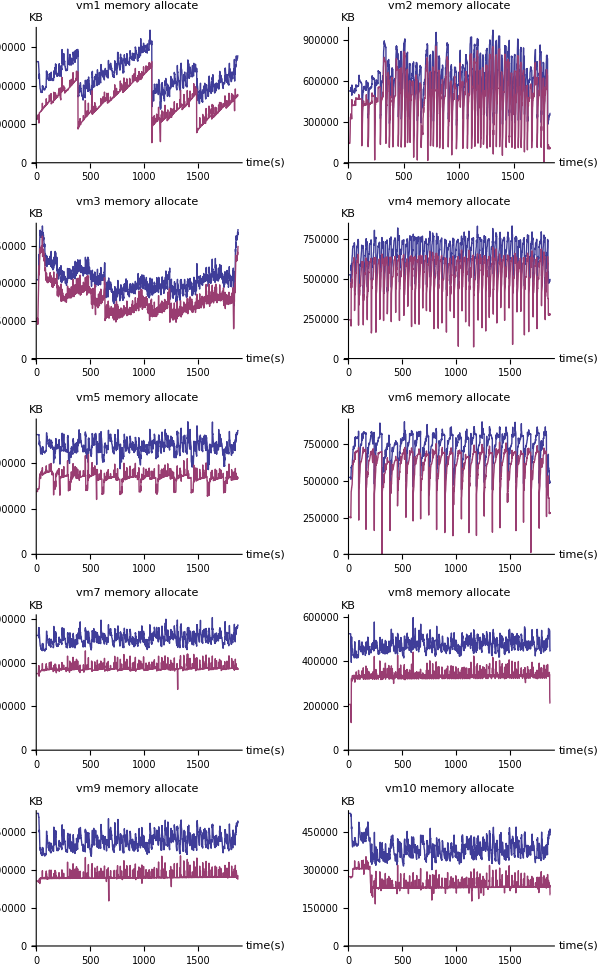

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

### 04-03 10 vm again

一共测试了2次,使用第二次结果.

N | 5G | init men | 512MB
vmcount | 10 | f | 120M

安排10台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | apache | cpu | 0 | Reqeust/s
vm2 | h2 | mem | 0 | ms
vm3 | build-linux-kernel | cpu | 0 | s
vm4 | tradebeans | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s
vm6 | tradesoap | mem | 100MB | ms
vm7 | john-the-ripper | cpu | 0 | real C/S
vm8 | scimark2 | cpu | 100MB | Mflops
vm9 | openssl | cpu | 0 | score
vm10 | crafty | cpu | 0 | s

选取这样10个测试是经过仔细考虑的,主要基于以下因素:

1. 尽可能的覆盖各种类型的测试
2. 体现实际服务器的各种用途的不同内存需求
3. 为了使得内存使用量区别开来,安排中间3台虚拟机使用了负载程序.
4. 不同时使用两个磁盘密集型程序,是为了保持测试能够顺利完成,当使用两个磁盘密集型程序之后,
    两个程序互相拖累,造成时间大幅度延长,两个测试分数对比开启调节之后都非常的低.
5. 虚拟机cpu是完全独立的分配的,所以测试项目的数量对整个结果没有影响.

下面是对各种测试的说明

### Apache ###

该测试是使用Apache的ab基准测试程序,该测试测量当处理700000个请求,并且保持100个执行并发请求.系统能够维持每秒种处理多少的请求.

该测试主要体现静态Web服务器的性能.

### h2 ###

执行和JDBCbench类似的内存数据库测试,使用一个银行程序的模型执行一定数量的事务.
h2是一个Java的SQL内存数据库

该测试主要体现内存数据库的性能.主要在一些高要求快速响应服务器中使用

### build-linux-kernel ###

该测试测量编译Linux 3.1 内核需要多长时间.

编译Linux内核是非常常用的测试,测试系统综合性能,直观方便.

### tradebeans and tradesoap ###

通过jave beans运行DayTrader基准测试,与H2作为内存中的Geronimo后端底层数据库
JavaBeans是一种规范，一种在Java（包括JSP）中使用可重复使用的Java组件的技术规范。其次，JavaBeans是一个Java的类.
Apache Geronimo 是 Apache 软件基金会的开放源码J2EE服务器
SOAP（Simple Object Access Protocol）简单对象访问协议,SOAP类似传统的二进制协议IIOP（CORBA）和JRMP（RMI），但它不采用二进制数据表示法，而是采用使用XML的，基于文本的数据表示法。

该项测试主要体现JAVA服务器的性能

### pgbench ###

该测试是一个简单的PostgreSQL的类似TPC-B基准测试.

是磁盘密集型程序,主要体现测试数据库的性能

### John-the-ripper ###

是一款密码破解程序,是cpu密集型程序,主要体现cpu性能

### scimark2 ###

用于测试科学和计算能力的基准工具

包括下面的项目

FFT:  Fast Foruier Transform  快速傅里叶变换

Jaccobi SOR:  Jacobi Successive Over-relaxation       逐次超松驰迭代法(连续过松弛算法)(Successive Over Relaxation Me thod,简称SOR方法)是高斯—塞德尔方法( Gauss–Seidel   method)的一种加速方法，是解大型稀疏矩阵方程组的有效方法之一，它具有计算公式简单，程序设计容易,占用计算机内存较少等优点,但需要较好的加速因子(即最佳松驰因子).   the Jacobi method 是其中的一个方法。

Monte Carlo： 蒙特卡罗算法  也称统计模拟方法，是二十世纪四十年代中期由于科学技术的发展和电子计算机的发明，而被提出的一种以概率统计理论为指导的一类非常重要的数值计算方法。是指使用随机数（或更常见的伪随机数）来解决很多计算问题的方法。与它对应的是确定性算法。

Sparse Matrix Multiply： 稀疏矩阵乘法，

 稀疏矩阵向量乘(Sparse Matrix-Vector Multiplication，SpMV)是科学计算领域一个非常重要的内核，在求解稀疏线性方程组的迭代法中占据了主要的计算量。SpMV计算y=Ax，其中A是规模为M×N的稀疏矩阵，x和y分别为长度为N和M的向量。

　　稀疏矩阵的元素大部分是零，非零元素所占比例往往小于元素总数的1%，因此，稀疏矩阵的存储往往采用压缩格式，只存储非零元和非零元在矩阵中的位置。在GPU上，HYB(HYBrid)是一种具有较高性能SpMV性能的稀疏矩阵存储格式，它使用ELL(ELLPACK)和COO(COOrdinate)两种存储格式来存储稀疏矩阵中非零元的信息。然而由于COO格式本身的特点，传统的SpMV算法只能串行计算，效率低下，并行化COO存储格式的SpMV算法对提高GPU上HYB格式的SpMV算法性能起到了很重要的作用。

dense LU matrix factorization： 稠密矩阵的LU分解计算， LU decomposition (also called LU factorization)

在线性代数中， LU分解是矩阵分解的一种，可以将一个矩阵分解为一个下三角矩阵和一个上三角矩阵的乘积（有时是它们和一个置换矩阵的乘积）。LU分解主要应用在数值分析中，用来解线性方程、求反矩阵或计算行列式。

主要测试面向科学计算的服务器性能,cpu集中型

### openssl ###

CPU集中型

### crafty ###

是一款棋类游戏的算法,CPU集中型.

```mathematica
{table,offraw,onraw}=Import["../dataset/4-02/statics.xlsx"];
label=table[[1,{2,3,4,5,6,7,8,11,17,18}]];
offswap=TableLoad[SwapLoad["4-02/vm"<>#<>"/off-swap.log"]&,10];
onswap=TableLoad[SwapLoad["4-02/vm"<>#<>"/on-swap.log"]&,10];
onmem=TableLoad[VMLoad["4-02/vm"<>#<>"/on-mem.log"]&,10];
```

以下是各个测试的具体成绩.
其中john-the-ripper有3组,最后一组没有正常运行完成所以分数无效.只取前两组.
scimark2有6组子成绩.

```mathematica
Grid[table[[1;;-2]]ᵀ,Frame->All]
```

id | sub id | intensive | load | unit | off | on
apache |  | cpu | 0. | request/s | 2987.47 | 2666.06
h2 |  | mem | 0. | ms | 120342. | 32328.3
Build-linux-kernel |  | cpu | 0. | s | 1057.5 | 1203.63
tradebeans |  | mem | 100M | ms | 25991.2 | 28541.1
pgbench |  | disk | 0. | TPS | 88.8258 | 103.918
tradesoap |  | mem | 100M | ms | 104163. | 102019.
John-the-ripper | Blowfish | cpu | 0. | real C/S | 564. | 530.333
 | Traditional DES | cpu | 0. | real C/S | 2.297×10^6 | 2.02833×10^6
 | MD5 | cpu | 0. | real C/S | 18196. | $Failed
scimark2 | Composite | cpu | 100M | Mflops | 410.125 | 408.655
 | Monte Carlo | cpu | 100M | Mflops | 161.74 | 159.443
 | Fast Fourier Transform | cpu | 100M | Mflops | 41.06 | 40.735
 | Sparse Matrix Multiply | cpu | 100M | Mflops | 451.07 | 449.98
 | Dense LU Matrix Factorization | cpu | 100M | Mflops | 974.828 | 961.228
 | Jacobi Successive Over-Relaxation | cpu | 100M | Mflops | 431.435 | 430.075
openssl |  | cpu | 0. | score | 52.0355 | 51.9184
crafty |  | cpu | 0. | s | 192.138 | 215.855

为了方便观察.制作了条形统计图.
并且使用几何平均,将john-the-ripper和scimark2的多组数据进行了合并.

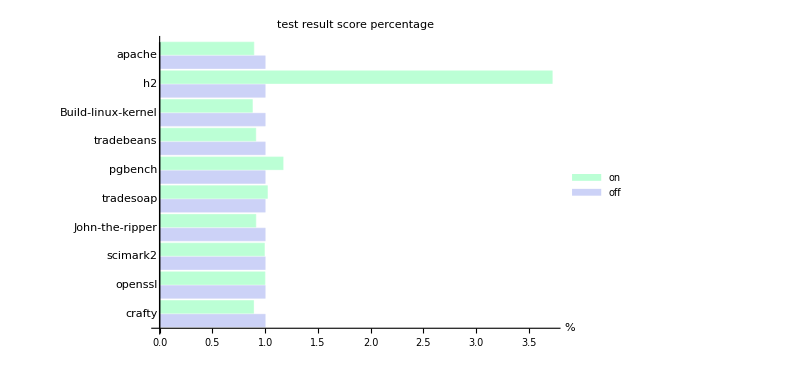

```mathematica
bar=
MakeList[table[[6,2;;7]],table[[7,2;;7]],{1,-1,-1,-1,1,-1}]~
Join~
{
{1,GeometricMean[table[[7,8;;9]]/table[[6,8;;9]]]},
{1,GeometricMean[table[[7,11;;16]]/table[[6,11;;16]]]}
}~
Join~
MakeList[table[[6,17;;18]],table[[7,17;;18]],{1,-1}];
BarChart[Reverse[bar],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{Reverse[label],None},AxesLabel->"%",BarOrigin->Left
]
```

可以看到分数差距最明显的是h2测试,因为该测试是完全的内存密集型,内存的多少对程序的执行具有非常明显的速度影响.

其次比较明显的是pgbench测试,因为该测试是磁盘密集型,当不开启调节的时候,各个虚拟机都大量的使用交换空间,消耗I/O带宽.
所以开启调节之后测试成绩反而有比较明显的提高.

剩下的测试分数都有所降低,在10%的范围内.

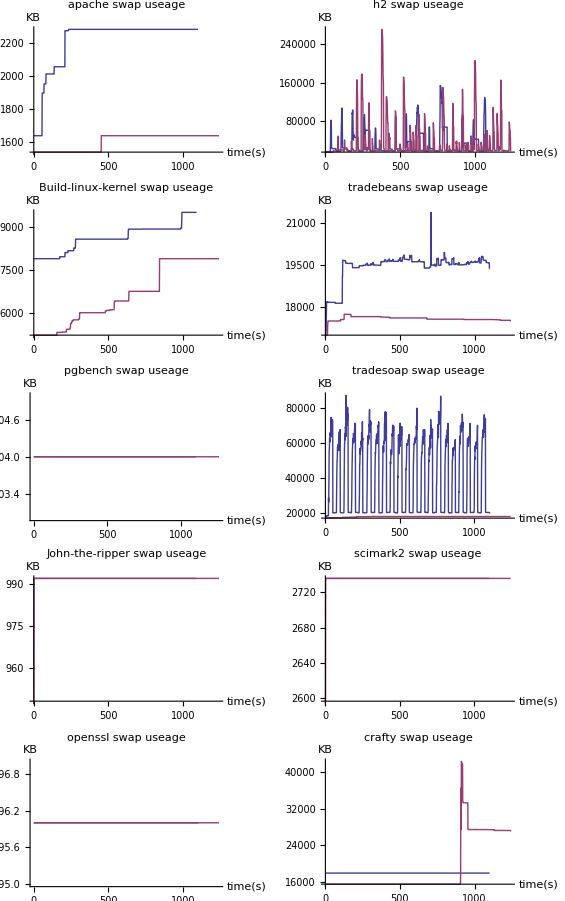

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->All,PlotLabel->label[[i]]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

从结果上可以看出:除了h2,tradebeans,tradesoap三个测试是大量的使用SWAP交换空间,其它的测试都没有使用交换空间.

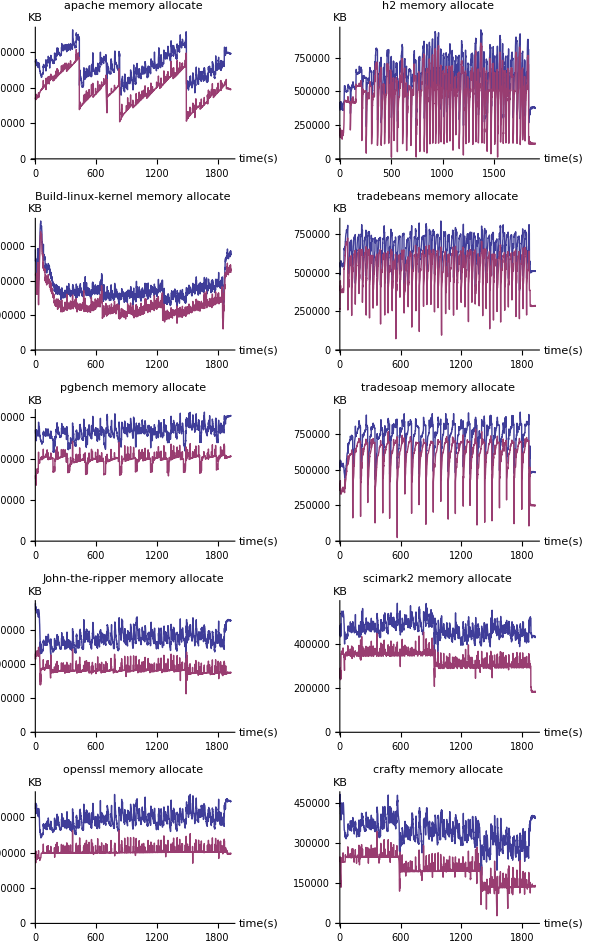

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->label[[i]]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```